# Quantum Smoothing

## Steady State/Resonance fluorescence Completely positive trajectories

Ivonne Guevara
Date of creation: 03.04.13
Last change:

```mathematica
$HistoryLength=1;
```

```mathematica
DateString[]
```

Wed 31 May 2017 16:26:54

```mathematica
ResetDirectory[]
(*SetDirectory["ownCloud/Quantum State Smoothing/PhD/QuantumSmoothing/codes/God/DataFromGod/dNdX"]
Directory[]*)
```

## Packages, Options, and simple functions

### Operators basis and definitions

Algebra of the 2x 2 Hilbert space: basic operators for an individual subsystem (I, σ_z, σ_-, σ_+).

```mathematica
Id={{1,0},{0,1}};Subscript[σ, x]={{0,1},{1,0}};Subscript[σ, y]={{0,-I},{I,0}};Subscript[σ, z]={{1,0},{0,-1}};Subscript[σ, m]=1/2(Subscript[σ, x]-I Subscript[σ, y]);Subscript[σ, p]=1/2(Subscript[σ, x]+I Subscript[σ, y]);
```

We define the commutator and anticommutator

```mathematica
Com[a_?MatrixQ,b_?MatrixQ]:=a.b-b.a
```

```mathematica
ACom[a_?MatrixQ,b_?MatrixQ]:=a.b+b.a
```

#### auxiliar Functions

```mathematica
Purity[a_?MatrixQ]:=Tr[a.a]
PurityEV[a_?MatrixQ]:=Module[
{λ, Λ},
λ=Eigenvalues[a];
Sum[λ[[j]]^2,{j,Length[λ]}]]
```

#### Higher dimensions

Hilbert space we define the tensor product.

```mathematica
CircleTimes[a_?MatrixQ,b_?MatrixQ]:=ArrayFlatten[Outer[Times,a,b]]
```

```mathematica
a⊗b//FullForm
```

CircleTimes[a,b]

We may now construct the operator basis for 2x2 Hilbert space.

```mathematica
Id2=Id⊗Id;
Subscript[σ, z1]=Subscript[σ, z]⊗Id;
Subscript[σ, z2]=Id⊗Subscript[σ, z];
Subscript[σ, m1]=Subscript[σ, m]⊗Id;
Subscript[σ, m2]=Id⊗Subscript[σ, m];
Subscript[σ, p1]=Subscript[σ, p]⊗Id;
Subscript[σ, p2]=Id⊗Subscript[S, p];
Subscript[σ, y1]=-I(Subscript[σ, p]-Subscript[σ, m])⊗Id;
Subscript[σ, y2]=Id⊗(-I(Subscript[σ, p]-Subscript[σ, m]));
```

Partial trace

```mathematica
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM])
```

### Parameters

For the non-unitary part of the dynamics we should define the jump operators describing the coupling of the system with the environment.

```mathematica
(*Solve[gg+GG==Apa&& gg==KK GG,{gg,GG}]*)
```

```mathematica
(*γpΓ=2;
γΓ=0.1;
γ=N[(γpΓ γΓ)/(1+γΓ)] (*decaying rate jumps Subscript[Δω, a]-i γ/2=-i∫Γ(τ)dτ *)
Γ=N[γpΓ-(γpΓ γΓ)/(1+γΓ)](*decaying rate diffusive trajectories*)*)
gG=1(*4/3*);
Υ =1(*3.5*)(*1*);
η=1/(1+gG)(*1.5/3.5*)(*10/11*);
Γ=N[Υ η]; (*Diffussion A*)
γ=N[Υ(1- η)]; (*Diffussion B*)
Φ=0(*N[Pi/2]*);(*local osc phase N[Pi/2](Y),0(X)*)
Ω=5(*10*)(*20*)(*γ+Γ*); (*Rabi oscillation*)
Δ=0(*0.5*)(*γ+Γ*); (*atom's effective detuning Δ=Subscript[ω, a]+Subscript[Δω, a]-Subscript[ω, 0]*)
n=0;(*thermal number of photons*)
h=0;
u=0 ;(*transformation jumps*)
β=0 ;(*transformation diff*)
```

```mathematica
γ+Γ
γ/Γ
γ
Γ
```

1.

1.

0.5

0.5

Initial and final times

```mathematica
ti=0;
tf=5;
```

Trajectories

```mathematica
traj=500(*number of QStrajectories in the ensemble*);
Ss=IntegerPart[(tf-ti)*3000]
dt=N[(tf-ti)/Ss];
```

15000

```mathematica
Export["variablestraj.h",{{"#define gA",γ},{"#define gB",Γ},{"#define phi",Φ},{"#define Omega",Ω},{"#define Delta",Δ},{"#define h",h},{"#define n",n},{"#define u", u},{"#define b",β},{"#define Smath",Ss},{"#define tmf",tf},{"#define tmi",ti}},"Table"]
```

variablestraj.h

```mathematica
(*Export["wjumps/Data1/variablestraj.h",{{"#define g",γ},{"#define G",Γ},{"#define phi",Φ},{"#define Omega",Ω},{"#define Delta",Δ},{"#define h",h},{"#define n",n},{"#define u", u},{"#define b",β},{"#define Smath",Ss},{"#define tmf",tf},{"#define tmi",ti}},"Table"]*)
```

### Hamiltonian and Lindbladians

The deterministic part of the dynamics is set by the system Hamiltonian

```mathematica
H=h Id+Ω/2 Subscript[σ, x]+Δ/2 Subscript[σ, z]
```

{{0,5/2},{5/2,0}}

```mathematica
cN=√(γ (n+1))Subscript[σ, m] (*Linbladians...Jump operators*)
```

{{0.,0.},{0.707107,0.}}

```mathematica
cy=√(Γ(n+1))E^(-I Φ)Subscript[σ, m] (*Linbladians...Trajectories operators*)
```

{{0.,0.},{0.707107,0.}}

Here we define the quantum expectation value operation (QEV)

```mathematica
PureQEV[O_?MatrixQ,x_]=Conjugate[x].O.x;
```

```mathematica
QEV[O_?MatrixQ,X_]=Norm[Re[Tr[O.X]]];
```

Here is how to evaluate the quantum expectation values of the jump operators

```mathematica
PureLQEV[x_]=PureQEV[#,x]&/@L;
```

```mathematica
LQEV[X_]=QEV[#,X]&/@L;
```

## Distributions

```mathematica
RandomBern[0]=0;
RandomBern[p_Real]:=RandomInteger[BernoulliDistribution[p]]
```

```mathematica
RandomNormal[0]=0;
RandomNormal[σ2_Real]:=RandomReal[NormalDistribution[0,√σ2]]
```

```mathematica
RandomNormal[0.7]
```

0.342345

### NonGaussian Distributed random variables (check cumulant.nb)

```mathematica
RandomPearson[μ_,μ2_,μ3_,μ4_]:=Module[{a0,aa0,a1,b0,bb0,b1,bb1,b2,bb2, aux},
a1=1;
aux=1/(2 (9 μ2^3+4 μ^3 μ3-16 μ μ2 μ3+6 μ3^2-5 μ2 μ4+μ^2 (-3 μ2^2+5 μ4)));
aa0=9 μ μ2^3-20 μ^2 μ2 μ3+3 μ2^2 μ3+8 μ μ3^2+(12 μ^3-13 μ μ2+μ3) μ4;
bb0= μ μ3 (μ2^2+μ4)+μ2 (3 μ3^2-4 μ2 μ4)+μ^2 (-4 μ3^2+3 μ2 μ4);
bb1=-3 μ μ2^3+8 μ^2 μ2 μ3-3 μ2^2 μ3-2 μ μ3^2-(6 μ^3-7 μ μ2+μ3) μ4;
bb2=3/5(-3 μ^2 μ2^2+4 μ2^3+4 μ^3 μ3-6 μ μ2 μ3+μ3^2);
a0=N[- aa0 aux];
b0= N[bb0 aux];
b1=N[bb1 aux];
b2=N[ 1/5+bb2 aux];
RandomReal[PearsonDistribution[a1,a0,b2,b1,b0]]

]
```

```mathematica
RandomPearsonA[A_,AA_,AAA_,dt_]:=Module[{a0,aa0,a1,b0,bb0,b1,bb1,b2,bb2, aux},
a1=1;
a0=N[ A dt +(-A^3+3 A AA-AAA/2) dt^2 ];
b0= N[dt (1-A^2 dt+2 AA dt)];
b1=N[(A^3-3 A AA) dt^2];
b2=N[ (-A^4+4 A^2 AA-2 AA^2) dt^2];
RandomReal[PearsonDistribution[a1,-a0,b2,b1,b0]]

]
```

## God

### ρ_G(0) and superoperators to order dt^2

Initial pure state

Steady State

```mathematica
cbs=N[1/(γ^2+2 Ω^2+4 Δ^2)];
xss=N[-4Ω γ cbs];
yss=N[2Ω γ cbs];
zss=N[(-γ^2-4 Δ^2)cbs];
ρss=0.5Id+xss Subscript[σ, x]+yss Subscript[σ, y]+zss Subscript[σ, z];
```

Pure State

```mathematica
Subscript[ψ, 0]={1,0};
```

```mathematica
ρ00=(*ρss*)Outer[Times,Conjugate[Subscript[ψ, 0]],Subscript[ψ, 0]]
```

{{1,0},{0,0}}

```mathematica
ReRho=Flatten@Re@ρ00;
ImRho=Flatten@Im@ρ00;
```

```mathematica
Export["Restate.dat",Table[ReRho[[j]],{j,1,4}],"List"]
```

Restate.dat

```mathematica
Export["Imstate.dat",Table[ImRho[[j]],{j,1,4}],"List"]
```

Imstate.dat

Superoperators

```mathematica
ρ[t_]=Table[Subscript[ρ,i,j][t],{i,1,2},{j,1,2}];
𝒥ρ[A_?MatrixQ,ρ_?MatrixQ]:=A.ρ.A†;
𝒟ρ[A_?MatrixQ,ρ_?MatrixQ]:=(A.ρ.A†-1/2(A†.A.ρ+ρ.A†.A));
ℒρ[A_?MatrixQ,ρ_?MatrixQ]:=-I Com[H,ρ[t]]+𝒟ρ[A,ρ];
𝒢ρ[A_?MatrixQ,ρ_?MatrixQ]:=If[Tr[A.ρ.A†]>0,((A.ρ.A†)/Tr[A.ρ.A†]-ρ),0];
ℋρ[A_?MatrixQ,ρ_?MatrixQ]:=(A.ρ+ρ.A†-Tr[A.ρ+ρ.A†]ρ);

(*ℐρ[A_?MatrixQ,ρ_?MatrixQ]:=2Tr[A.ρ](Tr[A.ρ]ρ-ℋρ[A,ρ])-(A.A.ρ+ρ.A.A);*)
```

### Measurement operators to order dt^2

```mathematica
UM[β_]:=({{1-dt/2 Abs[β]^2+dt^2/8 Abs[β]^4, β √dt}, {-β*√dt, 1-dt/2 Abs[β]^2+dt^2/8 Abs[β]^4}});
```

```mathematica
MM1[A_?MatrixQ]:=A √dt;
MM0[A_?MatrixQ]:=Id-1/2 A†.A dt-1/8(A†.A).(A†.A)dt^2;
```

```mathematica
M1[A_?MatrixQ,β_]:=(UM[β].{MM1[A],MM0[A]})[[1]];
M0[A_?MatrixQ,β_]:=(UM[β].{MM1[A],MM0[A]})[[2]];

My[A_?MatrixQ,dy_]:=Id+A dy-1/2(A†.A)dt-1/8(A†.A).(A†.A)dt^2;
```

```mathematica
MM0[cN]
```

{{0.999917,0.},{0.,1.}}

```mathematica
M0[cN,β]
```

{{0.999917,0.},{0.,1.}}

### Evolution operator

```mathematica
Eigensystem[-I H t]
```

{{(5 ⅈ t)/2,-(5 ⅈ t)/2},{{-1,1},{1,1}}}

```mathematica
λ[t_]=Eigenvalues[-I H t]
V[t_]=Transpose[Eigenvectors[-I H t]]
J=V[t].(-I H).Transpose[V[t]]
E^(J t)
-I H t
V[t].DiagonalMatrix[(λ [t])].Transpose[V[t]]
```

{(5 ⅈ t)/2,-(5 ⅈ t)/2}

{{-1,1},{1,1}}

{{5 ⅈ,0},{0,-5 ⅈ}}

{{ⅇ^(5 ⅈ t),1},{1,ⅇ^(-5 ⅈ t)}}

{{0,-(5 ⅈ t)/2},{-(5 ⅈ t)/2,0}}

{{0,-5 ⅈ t},{-5 ⅈ t,0}}

```mathematica
U[t_]=ExpToTrig@MatrixExp[-I H t](*(V[t].DiagonalMatrix[E^(λ [t])].Transpose[V[t]] ) *)(*Id-I H t-1/2 H.H t^2*)
U[0]
```

{{Cos[(5 t)/2],-ⅈ Sin[(5 t)/2]},{-ⅈ Sin[(5 t)/2],Cos[(5 t)/2]}}

{{1,0},{0,1}}

```mathematica
FullSimplify[ConjugateTranspose@U[t].U[t],Element[t ,Reals]]
FullSimplify[ConjugateTranspose@Chop@(Id-I H t-1/2 H.H t^2).Chop@(Id-I H t-1/2 H.H t^2),Element[t ,Reals]]
```

{{1,0},{0,1}}

{{1+(625 t^4)/64,0},{0,1+(625 t^4)/64}}

```mathematica
(*MatrixForm@Chop@TrigToExp[U[t]]
MatrixForm@Chop@(1/2 V[t].DiagonalMatrix[E^(λ [t])].Transpose[V[t]] )
MatrixForm@Chop@(Id-I H t-1/2 H.H t^2)*)
```

```mathematica
tp=dt;
N@FullSimplify@MatrixForm@Chop@(U[tp].ρ00.ConjugateTranspose@U[tp])
N@MatrixForm@Chop@(((Id-I H tp-1/2 H.H tp^2).ρ00.ConjugateTranspose@(Id-I H tp-1/2 H.H tp^2))/Tr[(Id-I H tp-1/2 H.H tp^2).ρ00.ConjugateTranspose@(Id-I H tp-1/2 H.H tp^2)])
```

(0.999999 | 0.+0.000833333 ⅈ
0.-0.000833333 ⅈ | 6.94444×10^-7)

(0.999999 | 0.+0.000833333 ⅈ
0.-0.000833333 ⅈ | 6.94444×10^-7)

### Exact analytical solution for dynamics

```mathematica
ρG[t_]=Module[
{ρtmp,Lρtmp,ρ0},
ρtmp=Flatten[ρ[t]];
Lρtmp=Flatten[-I Com[H,ρ[t]]+𝒟ρ[cy,ρ[t]]+𝒟ρ[cN,ρ[t]]];
ρ0=Flatten@ρ00;
ρ[t]/.
FullSimplify@Chop@Flatten@DSolve[(#[[1]]==#[[2]])&/@Flatten[(Transpose/@{{D[#,t]&/@ρtmp,Lρtmp},{ρtmp/.t->0,ρ0}}),1],ρtmp,t]
]
```

{{0.490196+(0.254902+0.0618421 ⅈ) ⅇ^((-0.75+4.99375 ⅈ) t)+(0.254902-0.0618421 ⅈ) ⅇ^((-0.75-4.99375 ⅈ) t),(0.-0.0980392 ⅈ)+(0.257675+0.0490196 ⅈ) ⅇ^((-0.75+4.99375 ⅈ) t)-(0.257675-0.0490196 ⅈ) ⅇ^((-0.75-4.99375 ⅈ) t)},{(0.+0.0980392 ⅈ)-(0.257675+0.0490196 ⅈ) ⅇ^((-0.75+4.99375 ⅈ) t)+(0.257675-0.0490196 ⅈ) ⅇ^((-0.75-4.99375 ⅈ) t),0.509804-(0.254902+0.0618421 ⅈ) ⅇ^((-0.75+4.99375 ⅈ) t)-(0.254902-0.0618421 ⅈ) ⅇ^((-0.75-4.99375 ⅈ) t)}}

```mathematica
DateString[]
time=Timing[Module[{data2,ρNG,ρNtemp},

SetSharedVariable[dataME];
(*data[[traj,S,(rho/dn/dy(*/lambdaN(pl)/PurityN/PurityNU/PurityNY*))]]*)
dataME={Table[ρ00,{s,1,Ss+1}]};
ρNG[1]=ρ00;
Do[ tt=ti+ss dt;
ρNG[s+1]=ρNG[s]+(𝒟ρ[cy,ρNG[s]]+𝒟ρ[cN,ρNG[s]]-I Com[H,ρNG[s]])dt+(𝒟ρ[cy†.cy,ρNG[s]]+𝒟ρ[cN†.cN,ρNG[s]])dt^2/4

,{s,1,Ss+1}];
dataME=Table[ρNG[s],{s,1,Ss+1}]
]][[1]]
```

Wed 31 May 2017 16:26:56

1.82318

### “Measurements” (N^↔)_G

```mathematica
dN[ρN_]:= Module[{p},
p=QEV[cN†.cN,ρN]dt;
RandomBern[p]
(*RandomInteger[BernoulliDistribution[p]]*)]
```

```mathematica
dNP[p_]:= RandomBern[p]
```

```mathematica
dN[ρ00]
```

0

```mathematica
(*u[t_]:={{1,0},{0,1}}*)
(*unravelling matrix*)
```

```mathematica
(*R[t_]:=Module[{uMatrix},
uMatrix=u[t];
ArrayFlatten[{{Id+Re[uMatrix],Im[uMatrix]},{Im[uMatrix],Id-Re[uMatrix]}}]
]*)
```

### “Measurements” Y^↔

```mathematica
dW[μ_,μ2_,μ3_,μ4_]:=RandomPearson[μ,μ2,μ3,μ4]
```

```mathematica
dWA[A_,AA_,AAA_,dt_]:=RandomPearsonA[A,AA,AAA,dt]
```

```mathematica
dWρ[ρNY__?MatrixQ,c_?MatrixQ]:=Module[{dw,A,AA,AAA,A2,μ,μ2,μ3,μ4},
A=Tr[ρNY.(c+c†)];
AAA=N[2Tr[ρNY.(c.c†.c)]];
AA=Tr[ρNY.(c.c†)];
A2=Tr[ρNY.(c)^2]-Tr[ρNY.(c†)^2];
(*μ=√Δt(A-Δt AAA);
μ2= 1+2 AA Δt;
μ3=3 √Δt μ;
μ4=3+12Δt AA;*)
μ=N[(A-dt/2 AAA)dt];
μ2= N[(1/dt+2 AA)dt^2 ];
μ3=N[3μ dt];
μ4=N[(3/dt^2+12/dt AA)dt^4];
dw=RandomPearson[μ,μ2,μ3,μ4]
]
```

### Ensemble of trajectories

#### Go

```mathematica
DateString[]
time=Timing[Module[{data2,purityNY,purityN,purityNU,ρNG,ρNYG,ρNYtemp,ρNU,ρNUtemp,ρNtemp,py,pnu,pl,MN,MY,dy,dNJG,dWJG,a0,b0,b1,b2,μ,μ2,μ3,μ4,A,AA,AAA,Ut,k,tt,ss,pn},
k=kf;
Ut=U[dt];
(*Do[ρNYG[0]=ρ00,{j,1,traj}];*)
SetSharedVariable[data];
(*data[[traj,S,(rho/dn/dy(*/lambdaN(pl)/PurityN/PurityNU/PurityNY*))]]*)
data={Table[{ρ00(*ρNYG[1,0]*),0,0(*,0,1,1,1*)},{s,0,Ss}]};
(*Do[Do[
Subscript[ρ, NY][j,0,k]=Subscript[ρ, 0],
{j,1,traj}
],{k,1,1}]*)
(*Do[*)
Do[ρNYG[1]=ρ00;ρNG[1]=ρNYG[1];ρNU[1]=ρNYG[1];
purityN[1]=Tr[ρNG[1].ρNG[1]];purityNU[1]=Tr[ρNU[1].ρNU[1]];purityNY[1]=Chop[Purity[ρNYG[1]]];
Do[ tt=ti+ss dt;
(*Jumps*)
ρNG[s]=ρNYG[s];
pl[s]=Re[Tr[cN†.cN.ρNG[s]]dt];
dNJG[s]=dNP[pl[s]];
MN=M1[cN,β]dNJG[s]+M0[cN,β](1-dNJG[s]);
ρNG[s+1]=𝒥ρ[MN,ρNG[s]];
pn=Tr[ ρNG[s+1]];
ρNtemp=ρNG[s+1]/pn;
ρNG[s+1]=ρNtemp;
purityN[s+1]=Tr[ρNG[s+1].ρNG[s+1]];
(*Hamiltonian Evolution*)
ρNU[s+1]=𝒥ρ[Ut,ρNG[s+1]];
ρNUtemp=ρNU[s+1];
pnu=Tr[ρNUtemp];
ρNU[s+1]=ρNUtemp/pnu;
purityNU[s+1]=Tr[ρNU[s+1].ρNU[s+1]];
(*Diffusive Trajectories*)
ρNYtemp=ρNU[s+1];
A=Re@N[Tr[ρNYtemp.(cy+cy†)]];
AAA=Re@N[Tr[ρNYtemp.(cy†.cy.cy)+ρNYtemp.(cy†.cy†.cy)]];
AA=Re@N[Tr[ρNYtemp.(cy†.cy)]];
(*A2=Re[N[Tr[Subscript[ρ, NYtemp].Subscript[c, Y].Subscript[c, Y]]-Tr[Subscript[ρ, NYtemp].Subscript[c, Y]†.Subscript[c, Y]†]]];*)

μ(*[j,s]*)=(A-dt/2 AAA)dt;(*E[ydt]*)
μ2(*[j,s]*)=(1/dt+2 AA)dt^2;(*E[(ydt)^2]*)
μ3(*[j,s]*)=3(μ(*[j,s]*))dt;(*E[(ydt)^3]*)
μ4(*[j,s]*)=(3/dt^2+12/dt AA)dt^4;(*E[(ydt)^3]*)
a0=N[ A dt +(-A^3+3 A AA-AAA/2) dt^2 ];
b0= N[dt (1-A^2 dt+2 AA dt)];
b1=Chop[N[(A^3-3 A AA) dt^2,dt^-2],dt];
b2=Chop[N[ (-A^4+4 A^2 AA-2 AA^2) dt^2,dt^-2],dt^2];
dWJG=RandomReal[PearsonDistribution[1,-a0,b2,b1,b0]];
(*Subscript[dWJ, G]=dWA(A,AA,AAA,dt);*)
(*Subscript[dWJ, G]=dW[μ(*[j,s]*),μ2(*[j,s]*),μ3(*[j,s]*),μ4(*[j,s]*)];*)
(*Subscript[dWJ, G]=dWρ[Subscript[ρ, NYtemp],Subscript[c, Y]];*)
dy[s]=(*μ*)(*[j,s]*)+dWJG;
MY=My[cy,dy[s]];
ρNYG[s+1]=𝒥ρ[MY,ρNYtemp];
ρNYtemp=ρNYG[s+1];
py=Tr[ρNYtemp];
ρNYG[s+1]=ρNYtemp/py;
purityNY[s+1]=Chop[Purity[ρNYG[s+1]]];
,{s,1,Ss+1}];
(*data[[traj,S,(rho/dn/dy(*/lambdaN(pl)/PurityN,PurityNU,PurityNY*))]]*)
data2=Table[{ρNYG[s],dNJG[s],dy[s](*,pl[j,s],purityN[j,s],purityNU[j,s],purityNY[j,s]*)},{s,1,Ss+1}];
AppendTo[data,data2];
,{j,1,traj}]
]
][[1]]
(*MemoryInUse[]
ClearAll[data2,purityNY,purityN,purityNU,ρNG,ρNYG,ρNYtemp,ρNU,ρNUtemp,ρNG,ρNtemp,py,pnu,pl,MN,MY,dy,dNJG,dWJG,a0,b0,b1,b2,μ,μ2,μ3,μ4,A,AA,AAA,Ut]*)
MemoryInUse[]
DateString[]
```

Wed 31 May 2017 16:26:59

3907.63578

2067534784

Wed 31 May 2017 17:33:13

```mathematica
(*data[[traj,S,(rho/dn/dy/lambdaN(pl)/PurityN,PurityNU,PurityNY)]]*)
```

```mathematica
data//Dimensions
data=Take[data,-traj];
data//Dimensions
```

{501,15001,3}

{500,15001,3}

### Results

#### Checking Pearson

```mathematica
(*ns=2;
MatrixForm[{{"μ","μ2","σ2","μ3","γ1","μ4","γ2"},{mu=μ[1,ns],
mu2=μ2[1,ns],
sigma2=mu2-mu^2,
mu3=μ3[1,ns],
gamma1=(mu3-3mu sigma2-mu^3)/(√sigma2)^3,
mu4=μ4[1,ns],
gamma2=Chop[(mu4-4mu mu3+6 mu^2 mu2-3 mu^4)/(sigma2)^2-3]}}]*)
```

```mathematica
(*aux=1/(2 (9 mu2^3+4 mu^3 mu3-16 mu mu2 mu3+6 mu3^2-5 mu2 mu4+mu^2 (-3 mu2^2+5 mu4)));
aa0=9 mu mu2^3-20 mu^2 mu2 mu3+3 mu2^2 mu3+8 mu mu3^2+(12 mu^3-13 mu mu2+mu3) mu4;
bb0= mu mu3 (mu2^2+mu4)+mu2 (3 mu3^2-4mu2 mu4)+mu^2 (-4 mu3^2+3 mu2 mu4);
bb1=-(3 mu mu2^3-8 mu^2 mu2 mu3+3 mu2^2 mu3+2 mu mu3^2+(6 mu^3-7 mu mu2+mu3) mu4);
bb2=3/5(-3 mu^2 mu2^2+4 mu2^3+4 mu^3 mu3-6 mu mu2 mu3+mu3^2);
a0=Chop[N[- aa0 aux]]
b0=Chop[ N[bb0 aux]]
b1=Chop[N[bb1 aux]]
b2=Chop[N[ 1/5+bb2 aux]]
*)
```

```mathematica
(*PearsonDistribution[1,a0,b2,b1,b0]*)
```

```mathematica
(*PDF[PearsonDistribution[1,a0,b2,b1,b0]]*)
```

```mathematica
(*(*NSamp=10^6;
dataP=RandomVariate[PearsonDistribution[1,a0,b2,b1,b0],NSamp];(*
Show[*)Histogram[dataP,{-300,300,0.05},"PDF"]*)(*,
(*Plot[PDF[NormalDistribution[Average[dt,a,aa,a2,b],Sigma[dt,a,aa,a2,b]],x],{x,-7,7},PlotStyle->{Orange}],Plot[PDF[PearsonDistribution[1,a0,b2,b1,b0],x],{x,-5,5}]*)]*)*)
```

```mathematica
(*DistributionParameterAssumptions[PearsonDistribution[1,A0,B0,B1,B2]]*)
```

#### Plots

Initialiazing plots

Wed 31 May 2017 16:05:27

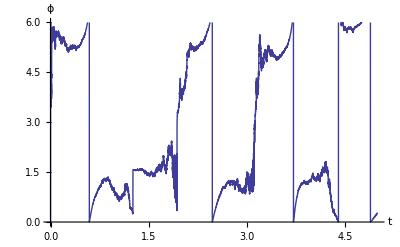

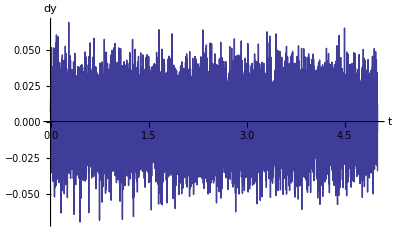

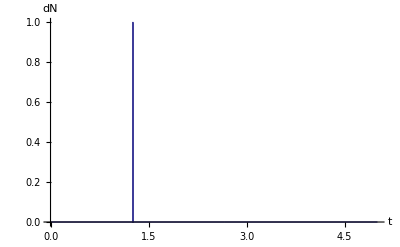

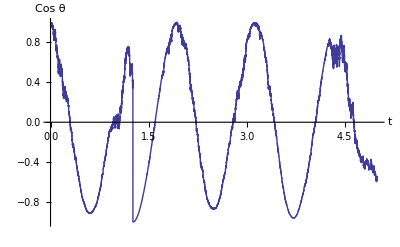

72846344

72845400

Wed 31 May 2017 16:05:39

```mathematica
(*DateString[]
phi[s_]:=Piecewise[{{Arg[data[[1,s,1]][[2,1]]]+2Pi,Arg[data[[1,s,1]][[2,1]]]<0},{Arg[data[[1,s,1]][[2,1]]],0≤Arg[data[[1,s,1]][[2,1]]]<2Pi},{Arg[data[[1,s,1]][[2,1]]]-2Pi,2Pi ≤ Arg[data[[1,s,1]][[2,1]]]}}];
PlotPhi=ListLinePlot[{Table[{s*dt,phi[s]},{s,1,Ss+1}]},PlotRange->{{0,5},{0,6}},AxesLabel->{t,"ϕ"}]
(*PlotlambdaN=ListLinePlot[Table[{s*dt,data[[1,s,4]]/dt},{s,1,Ss+1}],AxesLabel->{t,λ}];*)
Plotdy=ListLinePlot[Table[{s*dt,data[[1,s,3]]},{s,1,Ss+1}],AxesLabel->{t,dy}]
PlotdNJ=ListLinePlot[Table[{s*dt,data[[1,s,2]]},{s,1,Ss+1}],AxesLabel->{t,dN}]
(*PlotPurities=ListLinePlot[{Table[{s*dt,data[[1,s,5]]},{s,1,Ss+1}],Table[{s*dt,data[[1,s,6]]},{s,1,Ss+1}],Table[{s*dt,data[[1,s,7]]},{s,1,Ss+1}]},PlotRange->All,PlotLegends->{"Purity ρ_N","Purity ρ_NU","Purity ρ_NY"},AxesLabel->{t},AxesOrigin->{0,0}];*)PlotCos=ListLinePlot[{Table[{s*dt,Cos[2ArcTan[√((data[[1,s,1]][[2,2]])/(data[[1,s,1]][[1,1]]))]]},{s,1,Ss+1}]},PlotRange->All,AxesLabel->{t,"Cos θ"}]
MemoryInUse[]
ClearAll[phi,PlotPhi,Plotdy,PlotdNJ,PlotCos]
MemoryInUse[]
DateString[]*)
```

#### Export

All trajectories

```mathematica
DateString[]
timePrintAll=Timing[Module[{dyPrint,dNPrint,RerhoG,ImrhoG},
dyPrint=Flatten[data[[All,All,3]]];
dNPrint=Flatten[data[[All,All,2]]];
RerhoG=Flatten[Re@data[[All,All,1]]];
ImrhoG=Flatten[Im@data[[All,All,1]]];
Export["variablesgral.h",{{"#define QStrajmath",traj}},"Table"];
Export["dyB.dat",dyPrint];
Export["dNA.dat",dNPrint];
Export["ReRhoG.dat",RerhoG];
Export["ImRhoG.dat",ImrhoG];
]
][[1]]
MemoryInUse[]
DateString[]
```

Wed 31 May 2017 17:33:14

1354.84289

2066491368

Wed 31 May 2017 17:58:29

ME

```mathematica
(*DateString[]
timePrintAll=Timing[Module[{rhoGPrint},
rhoGPrint=Flatten[Table[{Re@ρG[s*dt][[1,1]],Re@ρG[s*dt][[1,2]],Im@ρG[s*dt][[1,2]],Re@ρG[s*dt][[2,2]]},{s,1,Ss+1}]];
Export["MERho.dat",rhoGPrint];
]
][[1]]
DateString[]*)
```

#### Selecting trajectories with one jump

```mathematica
(*DateString[]
timePrintwJump=(*Timing[*)Module[{SPrint,njump,Sint,s1,s2,(*temp,*)dimtemp,pos,(*selpos,*)dywJump,RerhoGwJump,ImrhoGwJump,dNwJump,times},
SPrint=Ss+1;
njump=1;Sint=IntegerPart[N[Ss/(tf-ti)]];
s1=Sint;s2=Ss-Sint;
temp=Select[data,(Total[#[[All,2]]]==njump)&];
dimtemp=Dimensions[Position[temp[[All,All,2]],1]][[1]];
pos =Position[temp[[All,All,2]],1];
times=Table[pos[[i,2]],{i,1,dimtemp}];
selpos=Select[pos,((#[[2]]>s1)&&(#[[2]]<s2))&];
timeswJump=selpos[[All,2]];
TrajwJump=Dimensions[selpos][[1]](*Dimensions@timeswJump[[1]]*);
siwJump=selpos[[All,2]]-Sint;
sfwJump=selpos[[All,2]]+Sint;
dataatjump=Table[temp[[selpos[[i,1]],siwJump[[i]](*selpos[[i,2]]-Sint*);;sfwJump[[i]](*selpos[[i,2]]+Sint*)]],{i,1,TrajwJump}];

datawjump=Table[temp[[selpos[[i,1]]]],{i,1,TrajwJump}];
dNwJump=Flatten[datawjump[[All,All,2]]];
dywJump=Flatten[datawjump[[All,All,3]]];
RerhoGwJump=Flatten[Re@datawjump[[All,All,1]]];
ImrhoGwJump=Flatten[Im@datawjump[[All,All,1]]];
Export["wjumps/variablesgral.h",{{"#define Sint",Sint},{"#define JumpSmath",N[2*Sint+1](*N[s2-s1]*)}},"Table"];
Export["wjumps/variablesgralwJumps2.h",{{"#define QStrajmath1",TrajwJump}},"Table"];
Export["wjumps/Data2/ImRhoGwJumps.dat",ImrhoGwJump];
Export["wjumps/Data2/dNwJumps.dat",dNwJump];
Export["wjumps/Data2/ReRhoGwJumps.dat",RerhoGwJump];
Export["wjumps/Data2/dywJumps.dat",dywJump];
Export["wjumps/Data2/StepsJumps.dat",timeswJump];
]
(*][[1]]*)
MemoryInUse[]
DateString[]
TrajwJump*)
```

```mathematica
(*Table[ListLinePlot[{Table[{s*dt,dataatjump[[mm,s,2]]},{s,1,6000}]},AxesLabel->{t,dN}],{mm,1,TrajwJump}]
Table[ListLinePlot[{Table[{s(**dt*),datawjump[[mm,s,2]]},{s,1,Ss}]},AxesLabel->{t,dN}],{mm,1,TrajwJump}]*)
```

## "ρ_Gmean(t)" (checking that we can recover the master equation)

```mathematica
(*k=1;*)
```

```mathematica
(*Subscript[ρ, NY][1000,5,1]*)
```

```mathematica
(*Subscript[ρ, NY][traj,1,1]*)
```

```mathematica
(*Subscript[ρ, NY][10000,1,2]*)
```

```mathematica
(*data[[traj,S,(rho/dn/dy(*/lambdaN(pl)/PurityN,PurityNU,PurityNY*))]]
dyPrint=Flatten[data[[All,All,3]]];
dNPrint=Flatten[data[[All,All,2]]];
RerhoG=Flatten[Re@data[[All,All,1]]];
ImrhoG=Flatten[Im@data[[All,All,1]]];*)

(*data=Table[{ρNYG[s],dNJG[s],dy[s]*)(*,pl[j,s],purityN[j,s],purityNU[j,s],purityNY[j,s]*)(*},{s,0,Ss}];*)
```

```mathematica
(*Do[ Ss=N[Ssi*10^k];dt=N[(tf-ti)/Ss];
Do[Subscript[ρ, Gmean][s,k]=Chop/@Mean[Table[Subscript[ρ, NY][j,s,k],{j,1,traj}]];,{s,0,Ss}],{k,k0,kf}]*)
```

```mathematica
(*data//Dimensions*)
```

```mathematica
(*Do[AvRhoG[s]=Mean[data[[All,s,1]]],{s,1,Ss+1}]*)
```

```mathematica
(*step=1;
AvRhoG[step]
Chop@ρG[(step-1)*dt]
dataME[[1]]*)
```

```mathematica
(*PlotAv={ListLinePlot[{Table[{s*dt,AvRhoG[s][[1,1]]},{s,1,Ss+1}],Table[{s*dt,ρG[s*dt][[1,1]]},{s,0,Ss}],(*Table[{s*dt,dataME[[s,1,1]]},{s,1,Ss+1}],*)Table[{s*dt,AvRhoG[s][[2,2]]},{s,1,Ss+1}],Table[{s*dt,Re@ρG[s*dt][[2,2]]},{s,0,Ss}],(*Table[{s*dt,dataME[[s,2,2]]},{s,1,Ss+1}]*)},AxesLabel->{t,ρ},PlotLegends->{"ρ_11","ρ_11^ME",(*"ρ_11MEdt",*)"ρ_22","ρ_22^ME"(*,"ρ_22MEdt"*)}, PlotRange->All,PlotStyle->{Normal,Dashed},PlotLabel->"Gtraj" traj],ListLinePlot[{Table[{s*dt,Re@AvRhoG[s][[1,2]]},{s,1,Ss+1}],Table[{s*dt,Re@ρG[s*dt][[1,2]]},{s,0,Ss}](*,Table[{s*dt,Re@dataME[[s,1,2]]},{s,1,Ss+1}]*),Table[{s*dt,Im@AvRhoG[s][[1,2]]},{s,1,Ss+1}],Table[{s*dt,Im@ρG[s*dt][[1,2]]},{s,0,Ss+1}](*,Table[{s*dt,Im@dataME[[s,1,2]]},{s,1,Ss+1}]*)},AxesLabel->{t,ρ},PlotLegends->{"Re(ρ_12)","Re(ρ_12^ME)"(*,"Re(ρ_12MEdt)"*),"Im(ρ_12)","Im(ρ_12^ME)"(*,"Im(ρ_21)MEdt"*)}, PlotRange->All,PlotStyle->{Normal,Dashed},PlotLabel->"Gtraj" traj]};*)
```

```mathematica
(*PlotAv[[1]]
PlotAv[[2]]*)
```

```mathematica
(*a=1;*)
```

```mathematica
(*MatrixForm[Subscript[ρ, Gmean][a,1]]
Tr[Subscript[ρ, Gmean][a,1]] 
Purity[Subscript[ρ, Gmean][a,1]]*)
```

```mathematica
(*MatrixForm[Chop[Subscript[ρ, G][a *0.1],10^-4]]
Chop@Tr[Subscript[ρ, G][a 0.1].Subscript[ρ, G][a 0.1]]*)
```

```mathematica
(*
 SsG=N[Ssi*10^kf];dtG=N[(tf-ti)/SsG];
PlotRhoGMean={};
PlotRhoG={ListLinePlot[{Table[{s*dtG,Subscript[ρ, G][s*dtG][[1,1]]},{s,0,SsG}],Table[{s*dtG,Re@Subscript[ρ, G][s*dtG][[1,2]]},{s,0,SsG}],Table[{s*dtG,Im@Subscript[ρ, G][s*dtG][[2,1]]},{s,0,SsG}],Table[{s*dtG,Subscript[ρ, G][s*dtG][[2,2]]},{s,0,SsG}]},AxesLabel->{t,ρ},PlotLegends->{"ρ_11","Im(ρ_12)","Re(ρ_21)","ρ_22"}, PlotRange->All]};
PlotDeltaRhoG={};
Do[ Ss=N[Ssi*10^k];dt=N[(tf-ti)/Ss];
PlotRhoGMean=AppendTo[PlotRhoGMean,ListLinePlot[{Table[{s*dt,Subscript[ρ, Gmean][s,k][[1,1]]},{s,0,Ss}],Table[{s*dt,Re@Subscript[ρ, Gmean][s,k][[1,2]]},{s,0,Ss}],Table[{s*dt,Im@Subscript[ρ, Gmean][s,k][[2,1]]},{s,0,Ss}],Table[{s*dt,Subscript[ρ, Gmean][s,k][[2,2]]},{s,0,Ss}]},AxesLabel->{t,ρ},PlotLegends->{"ρ_11","Im(ρ_12)","Re(ρ_21)","ρ_22"}]];
PlotDeltaRhoG=AppendTo[PlotDeltaRhoG,ListLinePlot[{Table[{s*dt,Subscript[ρ, G][s*dt][[1,1]]-Subscript[ρ, Gmean][s,k][[1,1]]},{s,0,Ss}],Table[{s*dt,Im@Subscript[ρ, G][s*dt][[1,2]]-Im@Subscript[ρ, Gmean][s,k][[1,2]]},{s,0,Ss}],Table[{s*dt,Re@Subscript[ρ, G][s*dt][[2,1]]-Re@Subscript[ρ, Gmean][s,k][[2,1]]},{s,0,Ss}],Table[{s*dt,Subscript[ρ, G][s*dt][[2,2]]-Subscript[ρ, Gmean][s,k][[2,2]]},{s,0,Ss}]},AxesLabel->{t,ρ},PlotLegends->{"Δρ_11","ΔIm(ρ_12)","ΔRe(ρ_21)","Δρ_22"}, PlotRange->All]];
,{k,k0,kf}]

PlotRhoGMean
PlotRhoG
PlotDeltaRhoG*)
```

```mathematica
(*PlotRhoG[[1]]*)
```

```mathematica
(*PlotRhoGMean[[1]]
PlotDeltaRhoG[[1]] 
PlotRhoGMean[[2]] 
PlotDeltaRhoG[[2]] 
PlotRhoGMean[[3]] 
PlotDeltaRhoG[[3]] *)
```

```mathematica
ClearAll["Global`*"]
```